# Molecular Dynamics

## Verlet Algorithm

```mathematica
V[x_]=1/2 k x^2;
F[x_]=-k x;
```

```mathematica
Subs={k->1,m->1}
```

{k→1,m→1}

```mathematica
time=10;
dt=0.1;
nSteps=Round[time/dt]
x0=-1;
```

100

```mathematica
x[0]=x0;
x[1]=x0+1/2 F[x[0]]/m  dt^2 /.Subs;
For[n=1,n<=nSteps,n++,
x[n+1]=2x[n]-x[n-1]+dt^2 F[x[n]]/m /.Subs
]
```

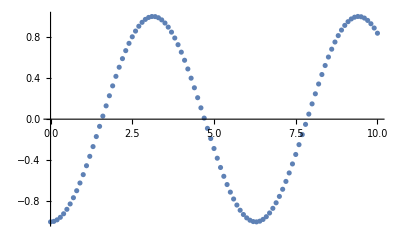

```mathematica
xData=Table[{n dt,x[n]},{n,0,nSteps}];
numPlot=ListPlot[xData]
```

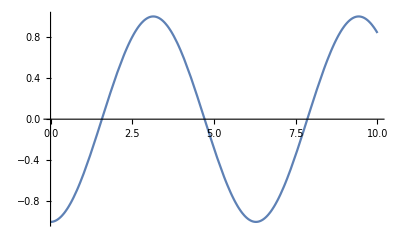

```mathematica
anaPlot=Plot[x0 Cos[Sqrt[k/m]t]/.Subs,{t,0,time}]
```

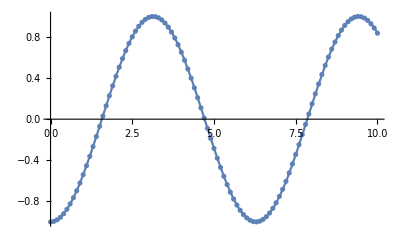

```mathematica
Show[numPlot,anaPlot]
```

## Velocity Verlet Algorithm

```mathematica
V[x_]=1/2 k x^2;
F[x_]=-k x;
```

```mathematica
Subs={k->1,m->1}
```

{k→1,m→1}

```mathematica
time=10;
dt=0.1;
nSteps=Round[time/dt]
x0=-1;
v0=0;
```

100

```mathematica
x[0]=x0;
v[0]=v0;
For[n=0,n<=nSteps,n++,
x[n+1]=x[n]+v[n]dt+dt^2 F[x[n]]/(2m) /.Subs;
v[n+1]=v[n]+(1/2)(F[x[n]]+F[x[n+1]])(dt/m)/.Subs;
]
```

```mathematica
xData=Table[{n dt,x[n]},{n,0,nSteps}];
numPlot=ListPlot[xData]
```

-Graphics-

```mathematica
anaPlot=Plot[x0 Cos[Sqrt[k/m]t]/.Subs,{t,0,time}]
```

-Graphics-

```mathematica
Show[numPlot,anaPlot]
```

-Graphics-

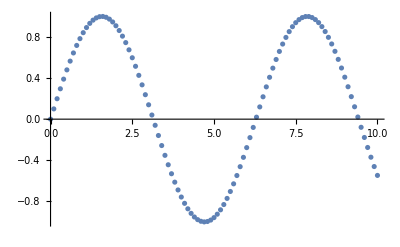

```mathematica
vData=Table[{n dt,v[n]},{n,0,nSteps}];
numvPlot=ListPlot[vData]
```



```mathematica
anavPlot=Plot[-x0 Sqrt[k/m]Sin[Sqrt[k/m]t]/.Subs,{t,0,time}]
```

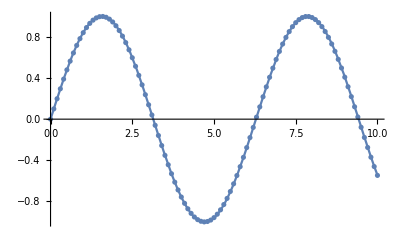

```mathematica
Show[numvPlot,anavPlot]
```

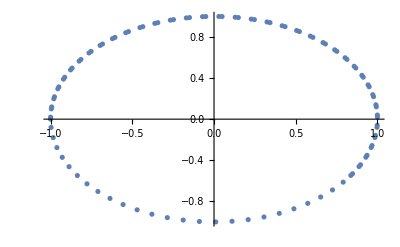

```mathematica
xvData=Table[{x[n],v[n]},{n,0,nSteps}];
ListPlot[xvData]
```

## Colinear dynamics

```mathematica
Vlj[r_]=4 ϵ((σ/r)^12-(σ/r)^6);
(*Flj[r_]=4 ϵ(12(σ^12/r^13)-6(σ^6/r^7));*)
Flj[r_]=24 ϵ(2(σ^12/r^13)-(σ^6/r^7));
```

```mathematica
Subs={ϵ->1,σ->1,mA->1,mB->1,mC->1}
```

{ϵ→1,σ→1,mA→1,mB→1,mC→1}

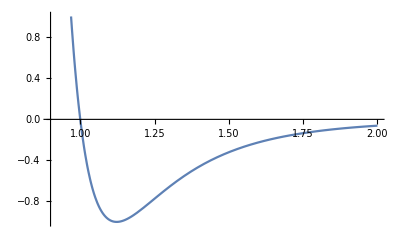

```mathematica
Plot[Vlj[r]/.Subs,{r,0.9,2}]
```

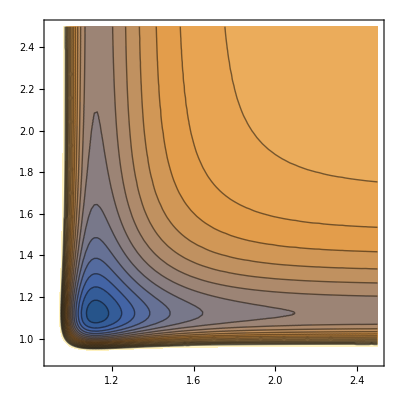

```mathematica
VPlot=ContourPlot[Vlj[rAB]+Vlj[rBC]+Vlj[rAB+rBC]/.Subs,{rAB,0.9,2.5},{rBC,0.9,2.5},Contours->20]
```

```mathematica
time=10;
dt=0.01;
nSteps=Round[time/dt]
```

1000

```mathematica
xA[0]=-2.5;
xB[0]=0;
xC[0]=1.1;
vA[0]=0.1;
vB[0]=0;
vC[0]=0;
fA[0]=-Flj[xB[0]-xA[0]]-Flj[xC[0]-xA[0]];
fB[0]=Flj[xB[0]-xA[0]]-Flj[xC[0]-xB[0]];
fC[0]=Flj[xC[0]-xA[0]]+Flj[xC[0]-xB[0]];
For[n=0,n<=nSteps,n++,
xA[n+1]=xA[n]+vA[n]dt+dt^2 fA[n]/(2mA) /.Subs;
xB[n+1]=xB[n]+vB[n]dt+dt^2 fB[n]/(2mB) /.Subs;
xC[n+1]=xC[n]+vC[n]dt+dt^2 fC[n]/(2mC) /.Subs;
fA[n+1]=-Flj[xB[n+1]-xA[n+1]]-Flj[xC[n+1]-xA[n+1]];
fB[n+1]=Flj[xB[n+1]-xA[n+1]]-Flj[xC[n+1]-xB[n+1]];
fC[n+1]=Flj[xC[n+1]-xA[n+1]]+Flj[xC[n+1]-xB[n+1]];
vA[n+1]=vA[n]+(1/2)(fA[n]+fA[n+1])(dt/mA)/.Subs;
vB[n+1]=vB[n]+(1/2)(fB[n]+fB[n+1])(dt/mB)/.Subs;
vC[n+1]=vC[n]+(1/2)(fC[n]+fC[n+1])(dt/mC)/.Subs;
]
```

```mathematica
trajData=Table[{xB[n]-xA[n],xC[n]-xB[n]},{n,0,nSteps}];
trajPlot=ListPlot[trajData,PlotStyle->Black];
```

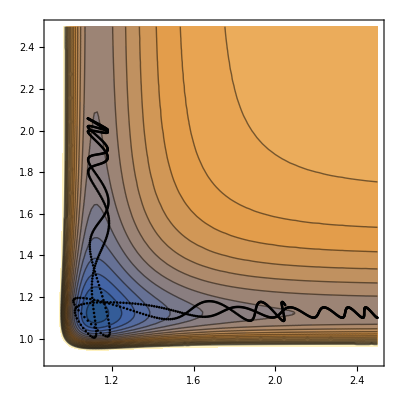

```mathematica
Show[VPlot,trajPlot]
```

```mathematica
Animate[ListPlot[{{xA[n],0},{xB[n],0},{xC[n],0}},PlotStyle->PointSize[0.1],PlotRange->{{-2.5,2.5},{-1,1}}],{n,0,nSteps,1}]
```

## 3N-D dynamics

```mathematica
Vlj1D[r_]=4 ϵ((σ/r)^12-(σ/r)^6);
Flj1D[r_]=24 ϵ(2(σ^12/r^13)-(σ^6/r^7));
```

```mathematica
Subs={ϵ->1,σ->1,m->1}
```

{ϵ→1,σ→1,m→1}

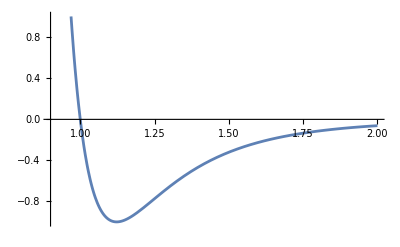

```mathematica
Plot[Vlj1D[r]/.Subs,{r,0.9,2}]
```

```mathematica
Vlj1D[1.2]/.Subs
```

-0.890965

```mathematica
Vlj3D[rij_]:=Module[{rijMag=Sqrt[rij.rij]},
Vlj1D[rijMag]/.Subs
]
```

```mathematica
r1={0,0,0};
r2={1.2,0,0};
r12=r2-r1;
Vlj3D[r12]
```

-0.890965

```mathematica
Flj3D[rij_]:=Module[{rijMag=Sqrt[rij.rij]},
Flj1D[rijMag]rij/rijMag/.Subs
];
```

```mathematica
Flj3D[r12]
```

{-2.21169,0.,0.}

```mathematica
Vlj[r_]:=Module[{i,j,nAtoms=Length[r],Vtot=0},
For[i=1,i<=nAtoms,i++,
For[j=i+1,j<=nAtoms,j++,
ri=r[[i]];
rj=r[[j]];
rij=rj-ri;
Vtot=Vtot+Vlj3D[rij];
];
];
Vtot
]
```

```mathematica
rtmp={{0,0,0},{1.2,0,0}};
Vlj[rtmp]
```

-0.890965

```mathematica
Flj[r_]:=Module[{i,j,nAtoms=Length[r],Ftot=0*r},
For[i=1,i<=nAtoms,i++,
For[j=i+1,j<=nAtoms,j++,
ri=r[[i]];
rj=r[[j]];
rij=rj-ri;
Ftot[[i]]=Ftot[[i]]-Flj3D[rij];
Ftot[[j]]=Ftot[[j]]+Flj3D[rij];
];
];
Ftot
]
```

```mathematica
rtmp={{0,0,0},{1.2,0,0}};
Flj[rtmp]
```

{{2.21169,0.,0.},{-2.21169,0.,0.}}

```mathematica
time=5.0;
dt=0.02;
nSteps=Round[time/dt]
```

250

```mathematica
r={{-5,0,0},{0,0,-1.1},{1.2,0,0},{-1.1,0,1.1},{0,1.1,0},{0,-1.2,0}};
v={{10,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}};
f=Flj[r];
rData={r};
For[n=0,n<nSteps,n++,
fold=f;
r=r+v dt+dt^2 f/(2m) /.Subs;
f=Flj[r];
v=v+(1/2)(fold+f)(dt/m)/.Subs;
rData=Append[rData,r];
]
```

## 3 D Visualizer

```mathematica
box=5;
trajData=rData;
Nsteps=Length[trajData];
Natoms=Length[trajData[[1]]];Animate[Graphics3D[{Blue,GraphicsComplex[trajData[[n]],Table[Sphere[i,0.5],{i,Natoms}]]},PlotRange->{{-box,box},{-box,box},{-box,box}},BoxRatios->{1,1,1},Axes->False],{n,1,nSteps,1}]
```